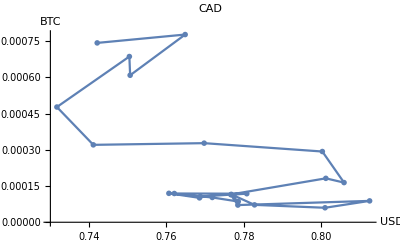

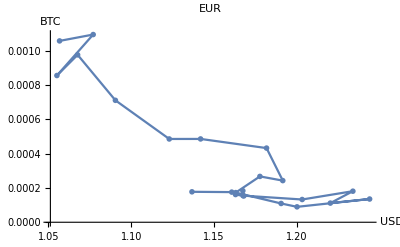

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data3= {curr1[[All,7]],curr2[[All,8]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data3->data3,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"CAD", AxesLabel->{"USD","BTC"}]

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data4 = {curr1[[All,11]],curr2[[All,12]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data4->data4,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"EUR", AxesLabel->{"USD","BTC"}]
```

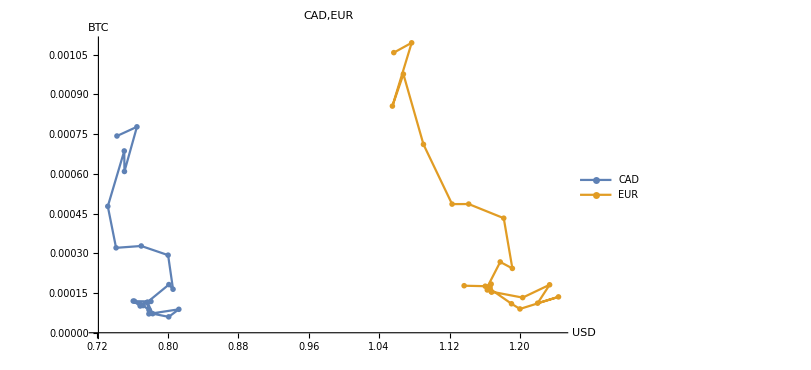

```mathematica
ListPlot[{data3,data4},Joined->True, PlotRange->All,PlotLegends-> {"CAD","EUR"}, PlotLabel->"CAD,EUR", AxesLabel->{"USD","BTC"},ImageSize->600,PlotMarkers->{●}]
```

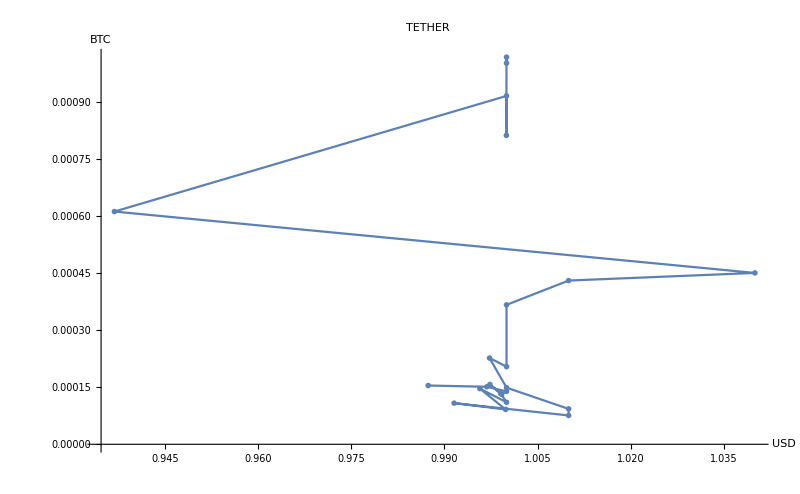

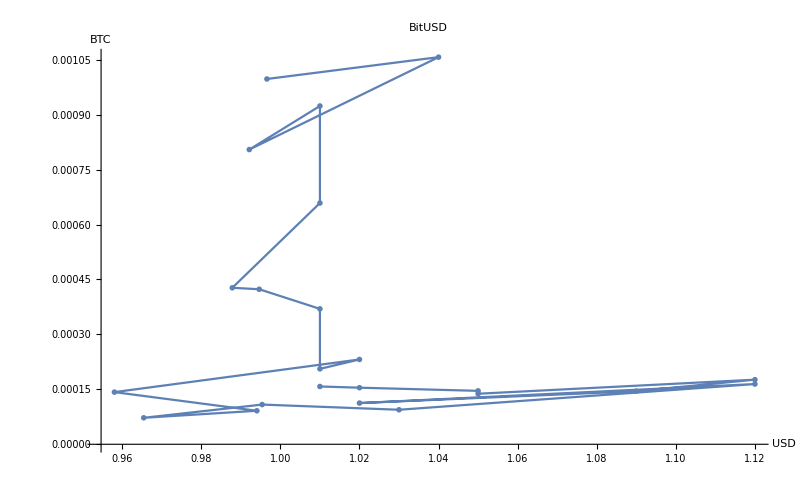

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data5 = {curr1[[All,21]],curr2[[All,22]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data5->data5,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"TETHER", AxesLabel->{"USD","BTC"}]

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data6 = {curr1[[All,23]],curr2[[All,24]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data6->data6,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"BitUSD", AxesLabel->{"USD","BTC"}]
```

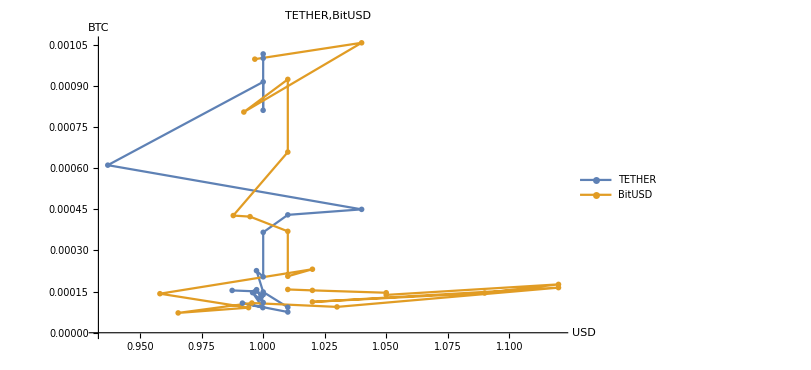

```mathematica
ListPlot[{data5,data6},Joined->True, PlotRange->All,PlotLegends-> {"TETHER","BitUSD"}, PlotLabel->"TETHER,BitUSD", AxesLabel->{"USD","BTC"},ImageSize->600,PlotMarkers->{●}]
```